```mathematica
Import?
```

```mathematica
?Import
```

Import[file] imports data from a file, returning a complete Mathematica version of it. 
Import[file,elements] imports the specified elements from a file.
Import[http://url,…] and Import[ftp://url,…] imports from any accessible URL.

```mathematica
Import["/Users/alexis/Desktop/results.csv"]
```

{{length , alphabetsize , numOfColors , cluster_size , perimeter_of_the_cluster , number_of_unique_colors },{8,2,50,1.194,9.1265,8.3515},{8,2,49,1.1855,9.079,8.268},{8,2,48,1.1925,9.113,8.3235},{8,2,47,1.209,9.2085,8.3425},{8,2,46,1.218,9.262,8.3765},{8,2,45,1.19,9.0905,8.245},{8,2,44,1.215,9.2425,8.358},{8,2,43,1.2305,9.33,8.408},{8,2,42,1.23,9.3285,8.346},{8,2,41,1.22,9.262,8.2875},{8,2,40,1.2395,9.3765,8.3305},{8,2,39,1.243,9.4055,8.286},{8,2,38,1.266,9.5285,8.3585},{8,2,37,1.2675,9.533,8.3585},{8,2,36,1.298,9.697,8.437},{8,2,35,1.287,9.647,8.389},{8,2,34,1.282,9.609,8.305},{8,2,33,1.3155,9.788,8.4005},{8,2,32,1.311,9.769,8.3725},{8,2,31,1.336,9.8895,8.345},{8,2,30,1.355,10.012,8.42},{8,2,29,1.3505,9.975,8.306},{8,2,28,1.345,9.961,8.3055},{8,2,27,1.3775,10.12,8.3005},{8,2,26,1.3935,10.2145,8.2515},{8,2,25,1.4345,10.4235,8.339},{8,2,24,1.4675,10.586,8.327},{8,2,23,1.461,10.5775,8.2915},{8,2,22,1.5195,10.8835,8.3145},{8,2,21,1.5305,10.935,8.2205},{8,2,20,1.5975,11.2685,8.2335},{8,2,19,1.616,11.379,8.1775},{8,2,18,1.699,11.8075,8.184},{8,2,17,1.7625,12.1115,8.1165},{8,2,16,1.8125,12.365,8.0295},{8,2,15,1.951,13.0485,8.0175},{8,2,14,2.0305,13.4315,7.8515},{8,2,13,2.143,14.02,7.7305},{8,2,12,2.38,15.1005,7.583},{8,2,11,2.6815,16.5145,7.357},{8,2,10,2.8935,17.496,6.9955},{8,2,9,3.6,20.5865,6.5985},{8,2,8,4.296,23.487,6.092},{8,2,7,6.1265,30.78,5.519},{8,2,6,9.536,42.912,4.763},{8,2,5,18.2665,69.217,3.9315},{8,2,4,40.227,117.661,2.9895},{8,2,3,76.671,151.496,1.9995}}

```mathematica
results = Import["/Users/alexis/Desktop/results.csv"]
```

{{length , alphabetsize , numOfColors , cluster_size , perimeter_of_the_cluster , number_of_unique_colors },{8,2,50,1.194,9.1265,8.3515},{8,2,49,1.1855,9.079,8.268},{8,2,48,1.1925,9.113,8.3235},{8,2,47,1.209,9.2085,8.3425},{8,2,46,1.218,9.262,8.3765},{8,2,45,1.19,9.0905,8.245},{8,2,44,1.215,9.2425,8.358},{8,2,43,1.2305,9.33,8.408},{8,2,42,1.23,9.3285,8.346},{8,2,41,1.22,9.262,8.2875},{8,2,40,1.2395,9.3765,8.3305},{8,2,39,1.243,9.4055,8.286},{8,2,38,1.266,9.5285,8.3585},{8,2,37,1.2675,9.533,8.3585},{8,2,36,1.298,9.697,8.437},{8,2,35,1.287,9.647,8.389},{8,2,34,1.282,9.609,8.305},{8,2,33,1.3155,9.788,8.4005},{8,2,32,1.311,9.769,8.3725},{8,2,31,1.336,9.8895,8.345},{8,2,30,1.355,10.012,8.42},{8,2,29,1.3505,9.975,8.306},{8,2,28,1.345,9.961,8.3055},{8,2,27,1.3775,10.12,8.3005},{8,2,26,1.3935,10.2145,8.2515},{8,2,25,1.4345,10.4235,8.339},{8,2,24,1.4675,10.586,8.327},{8,2,23,1.461,10.5775,8.2915},{8,2,22,1.5195,10.8835,8.3145},{8,2,21,1.5305,10.935,8.2205},{8,2,20,1.5975,11.2685,8.2335},{8,2,19,1.616,11.379,8.1775},{8,2,18,1.699,11.8075,8.184},{8,2,17,1.7625,12.1115,8.1165},{8,2,16,1.8125,12.365,8.0295},{8,2,15,1.951,13.0485,8.0175},{8,2,14,2.0305,13.4315,7.8515},{8,2,13,2.143,14.02,7.7305},{8,2,12,2.38,15.1005,7.583},{8,2,11,2.6815,16.5145,7.357},{8,2,10,2.8935,17.496,6.9955},{8,2,9,3.6,20.5865,6.5985},{8,2,8,4.296,23.487,6.092},{8,2,7,6.1265,30.78,5.519},{8,2,6,9.536,42.912,4.763},{8,2,5,18.2665,69.217,3.9315},{8,2,4,40.227,117.661,2.9895},{8,2,3,76.671,151.496,1.9995}}

```mathematica
results
```

{{length , alphabetsize , numOfColors , cluster_size , perimeter_of_the_cluster , number_of_unique_colors },{8,2,50,1.194,9.1265,8.3515},{8,2,49,1.1855,9.079,8.268},{8,2,48,1.1925,9.113,8.3235},{8,2,47,1.209,9.2085,8.3425},{8,2,46,1.218,9.262,8.3765},{8,2,45,1.19,9.0905,8.245},{8,2,44,1.215,9.2425,8.358},{8,2,43,1.2305,9.33,8.408},{8,2,42,1.23,9.3285,8.346},{8,2,41,1.22,9.262,8.2875},{8,2,40,1.2395,9.3765,8.3305},{8,2,39,1.243,9.4055,8.286},{8,2,38,1.266,9.5285,8.3585},{8,2,37,1.2675,9.533,8.3585},{8,2,36,1.298,9.697,8.437},{8,2,35,1.287,9.647,8.389},{8,2,34,1.282,9.609,8.305},{8,2,33,1.3155,9.788,8.4005},{8,2,32,1.311,9.769,8.3725},{8,2,31,1.336,9.8895,8.345},{8,2,30,1.355,10.012,8.42},{8,2,29,1.3505,9.975,8.306},{8,2,28,1.345,9.961,8.3055},{8,2,27,1.3775,10.12,8.3005},{8,2,26,1.3935,10.2145,8.2515},{8,2,25,1.4345,10.4235,8.339},{8,2,24,1.4675,10.586,8.327},{8,2,23,1.461,10.5775,8.2915},{8,2,22,1.5195,10.8835,8.3145},{8,2,21,1.5305,10.935,8.2205},{8,2,20,1.5975,11.2685,8.2335},{8,2,19,1.616,11.379,8.1775},{8,2,18,1.699,11.8075,8.184},{8,2,17,1.7625,12.1115,8.1165},{8,2,16,1.8125,12.365,8.0295},{8,2,15,1.951,13.0485,8.0175},{8,2,14,2.0305,13.4315,7.8515},{8,2,13,2.143,14.02,7.7305},{8,2,12,2.38,15.1005,7.583},{8,2,11,2.6815,16.5145,7.357},{8,2,10,2.8935,17.496,6.9955},{8,2,9,3.6,20.5865,6.5985},{8,2,8,4.296,23.487,6.092},{8,2,7,6.1265,30.78,5.519},{8,2,6,9.536,42.912,4.763},{8,2,5,18.2665,69.217,3.9315},{8,2,4,40.227,117.661,2.9895},{8,2,3,76.671,151.496,1.9995}}

```mathematica
results2 = Table[results[[i]],{i,2,Length[results]}]
```

```mathematica
{{8,2,50,1.194,9.1265,8.3515},{8,2,49,1.1855,9.079,8.268},{8,2,48,1.
1925,9.113,8.3235},{8,2,47,1.209,9.2085,8.3425},{8,2,46,1.218,9.262,8.3765},{8,2,45,1.19,9.0905,8.245},{8,2,44,1.215,9.2425,8.358},{8,2,43,1.2305,9.33,8.408},{8,2,42,1.23,9.3285,8.346},{8,2,41,1.22,9.262,8.2875},{8,2,40,1.2395,9.3765,8.3305},{8,2,39,1.243,9.4055,8.286},{8,2,38,1.266,9.5285,8.3585},{8,2,37,1.2675,9.533,8.3585},{8,2,36,1.298,9.697,8.437},{8,2,35,1.287,9.647,8.389},{8,2,34,1.282,9.609,8.305},{8,2,33,1.3155,9.788,8.4005},{8,2,32,1.311,9.769,8.3725},{8,2,31,1.336,9.8895,8.345},{8,2,30,1.355,10.012,8.42},{8,2,29,1.3505,9.975,8.306},{8,2,28,1.345,9.961,8.3055},{8,2,27,1.3775,10.12,8.3005},{8,2,26,1.3935,10.2145,8.2515},{8,2,25,1.4345,10.4235,8.339},{8,2,24,1.4675,10.586,8.327},{8,2,23,1.461,10.5775,8.2915},{8,2,22,1.5195,10.8835,8.3145},{8,2,21,1.5305,10.935,8.2205},{8,2,20,1.5975,11.2685,8.2335},{8,2,19,1.616,11.379,8.1775},{8,2,18,1.699,11.8075,8.184},{8,2,17,1.7625,12.1115,8.1165},{8,2,16,1.8125,12.365,8.0295},{8,2,15,1.951,13.0485,8.0175},{8,2,14,2.0305,13.4315,7.8515},{8,2,13,2.143,14.02,7.7305},{8,2,12,2.38,15.1005,7.583},{8,2,11,2.6815,16.5145,7.357},{8,2,10,2.8935,17.496,6.9955},{8,2,9,3.6,20.5865,6.5985},{8,2,8,4.296,23.487,6.092},{8,2,7,6.1265,30.78,5.519},{8,2,6,9.536,42.912,4.763},{8,2,5,18.2665,69.217,3.9315},{8,2,4,40.227,117.661,2.9895},{8,2,3,76.671,151.4955,1.9995}}
```

{{8,2,50,1.194,9.1265,8.3515},{8,2,49,1.1855,9.079,8.268},{8,2,48,1925.,9.113,8.3235},{8,2,47,1.209,9.2085,8.3425},{8,2,46,1.218,9.262,8.3765},{8,2,45,1.19,9.0905,8.245},{8,2,44,1.215,9.2425,8.358},{8,2,43,1.2305,9.33,8.408},{8,2,42,1.23,9.3285,8.346},{8,2,41,1.22,9.262,8.2875},{8,2,40,1.2395,9.3765,8.3305},{8,2,39,1.243,9.4055,8.286},{8,2,38,1.266,9.5285,8.3585},{8,2,37,1.2675,9.533,8.3585},{8,2,36,1.298,9.697,8.437},{8,2,35,1.287,9.647,8.389},{8,2,34,1.282,9.609,8.305},{8,2,33,1.3155,9.788,8.4005},{8,2,32,1.311,9.769,8.3725},{8,2,31,1.336,9.8895,8.345},{8,2,30,1.355,10.012,8.42},{8,2,29,1.3505,9.975,8.306},{8,2,28,1.345,9.961,8.3055},{8,2,27,1.3775,10.12,8.3005},{8,2,26,1.3935,10.2145,8.2515},{8,2,25,1.4345,10.4235,8.339},{8,2,24,1.4675,10.586,8.327},{8,2,23,1.461,10.5775,8.2915},{8,2,22,1.5195,10.8835,8.3145},{8,2,21,1.5305,10.935,8.2205},{8,2,20,1.5975,11.2685,8.2335},{8,2,19,1.616,11.379,8.1775},{8,2,18,1.699,11.8075,8.184},{8,2,17,1.7625,12.1115,8.1165},{8,2,16,1.8125,12.365,8.0295},{8,2,15,1.951,13.0485,8.0175},{8,2,14,2.0305,13.4315,7.8515},{8,2,13,2.143,14.02,7.7305},{8,2,12,2.38,15.1005,7.583},{8,2,11,2.6815,16.5145,7.357},{8,2,10,2.8935,17.496,6.9955},{8,2,9,3.6,20.5865,6.5985},{8,2,8,4.296,23.487,6.092},{8,2,7,6.1265,30.78,5.519},{8,2,6,9.536,42.912,4.763},{8,2,5,18.2665,69.217,3.9315},{8,2,4,40.227,117.661,2.9895},{8,2,3,76.671,151.496,1.9995}}

```mathematica
data = Table[{results2[[i]][[3]],results2[[i]][[6]]},{i,1,Length[results2]}]
```

{{50,8.3515},{49,8.268},{48,8.3235},{47,8.3425},{46,8.3765},{45,8.245},{44,8.358},{43,8.408},{42,8.346},{41,8.2875},{40,8.3305},{39,8.286},{38,8.3585},{37,8.3585},{36,8.437},{35,8.389},{34,8.305},{33,8.4005},{32,8.3725},{31,8.345},{30,8.42},{29,8.306},{28,8.3055},{27,8.3005},{26,8.2515},{25,8.339},{24,8.327},{23,8.2915},{22,8.3145},{21,8.2205},{20,8.2335},{19,8.1775},{18,8.184},{17,8.1165},{16,8.0295},{15,8.0175},{14,7.8515},{13,7.7305},{12,7.583},{11,7.357},{10,6.9955},{9,6.5985},{8,6.092},{7,5.519},{6,4.763},{5,3.9315},{4,2.9895},{3,1.9995}}

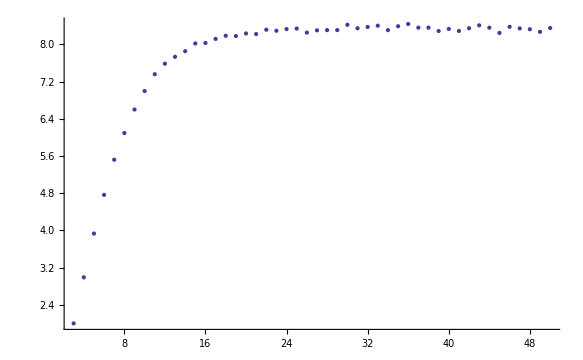

```mathematica
ListPlot[data,PlotRange->All]
```

```mathematica
data2 = Table[{results2[[i]][[3]],results2[[i]][[4]]},{i,1,Length[results2]}]
```

{{50,1.194},{49,1.1855},{48,1.1925},{47,1.209},{46,1.218},{45,1.19},{44,1.215},{43,1.2305},{42,1.23},{41,1.22},{40,1.2395},{39,1.243},{38,1.266},{37,1.2675},{36,1.298},{35,1.287},{34,1.282},{33,1.3155},{32,1.311},{31,1.336},{30,1.355},{29,1.3505},{28,1.345},{27,1.3775},{26,1.3935},{25,1.4345},{24,1.4675},{23,1.461},{22,1.5195},{21,1.5305},{20,1.5975},{19,1.616},{18,1.699},{17,1.7625},{16,1.8125},{15,1.951},{14,2.0305},{13,2.143},{12,2.38},{11,2.6815},{10,2.8935},{9,3.6},{8,4.296},{7,6.1265},{6,9.536},{5,18.2665},{4,40.227},{3,76.671}}

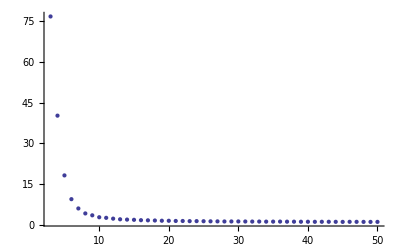

```mathematica
ListPlot[data2]
```

```mathematica
?ListLogLogPlot
```

ListLogLogPlot[{{x_1,y_1},{x_2,y_2},…}] makes a log-log plot of the specified list of x and y values.
ListLogLogPlot[{list_1,list_2,…}] plots several lists of values.

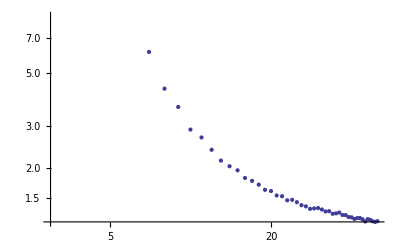

```mathematica
ListLogLogPlot[data2]
```